#### Final Exam - Oral

### Load packages

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

### Final Exam - Oral

#### Q1

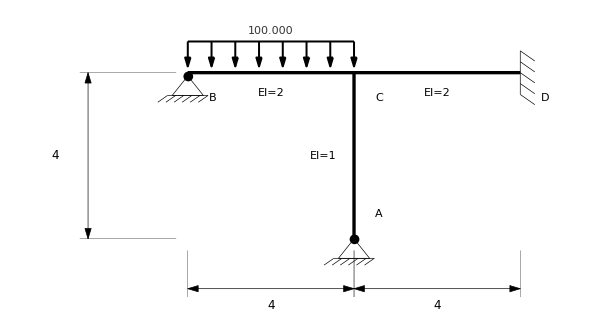

a - Sketch the deformation and the moment diagram of all members.
b - Describe how you would obtain the moment diagram
c - Demonstrate and identify the formulas that would allow you to obtain the moments at all endpoints and the maximum moment in member BC.

#### Q2

Briefly answer the following questions:

A. For an ideal I-beam, the plastic moment is equal to the yield moment.  Explain why this happens.  Also explain why the plastic moment is NOT equal to the yield moment for a rectangular section.
B. Under what condition should an engineer choose a rectangular section instead of an I-beam when designing against plastic collapse.  Explain.
C. The plastic shape factor is 50% higher for a rectangular cross-section than for an ideal I-beam. Does that mean that a rectangular cross-section is more efficient than an ideal I-beam cross-section under plastic collapse? Explain.

## Answers

#### Q1

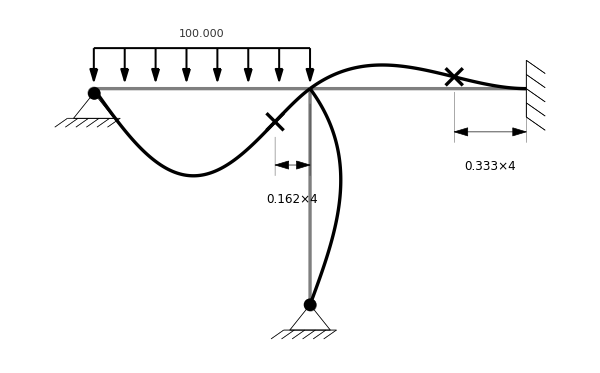
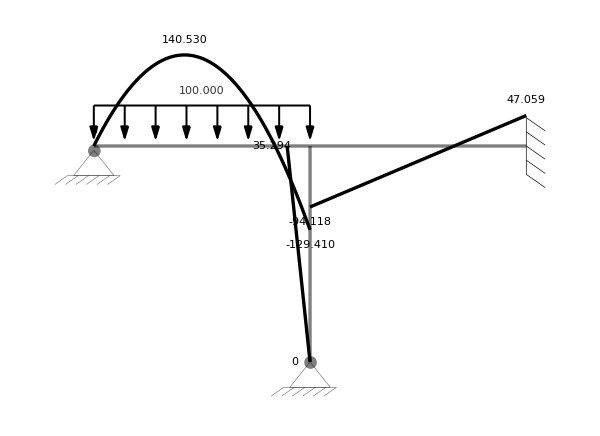
-Graphics-
-Graphics-
-Graphics-

#### Q2

A. This happens because the flanges yield first and once the flanges yield, then all the material in the cross-section has yielded because all the material in an ideal beam is in the flanges and there is no additional reserve capacity.  
For the rectangular beam, when the material yields at the top and bottom of the cross-section, the inner part has not yielded and provides additional reserve capacity for yielding so that the moment has to increase in order to yield the rest of the cross-section.

B. If an engineer is prioritizing having large deformations before collapse (called fail-safe design) so that after initial yielding, we get significant deformation with reserve capacity then a rectangular section is preferred.  A rectangular section requires twice as much weight for the same load so an intermediate section between an I-beam and a rectangular section may often be preferred.

C. No, for the same cross-sectional area and total height, the I-beam has a higher plastic moment than a rectangular cross-section. Therefore for a beam member with the same weight and height as a rectangular cross-section (or square), the plastic moment of an I-beam cross-section can carry more load before plastic collapse. However, the ratio of plastic moment to the yield moment, which is the plastic shape factor, is higher for a rectangular cross-section.

## Preparation

Q1

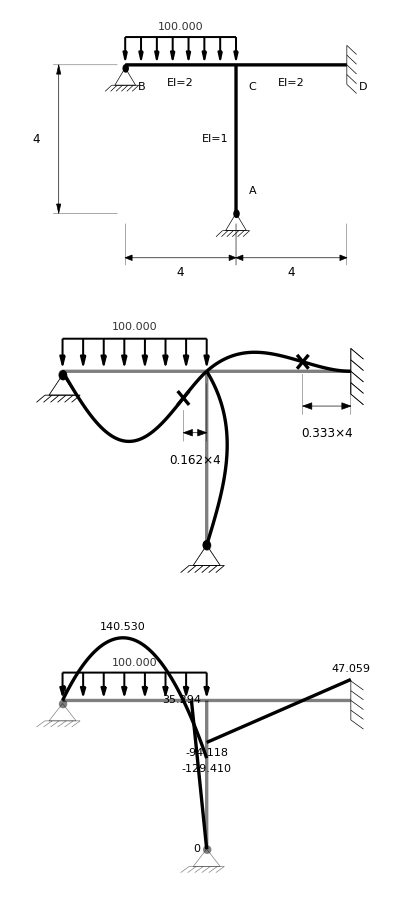

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4},600,
buildingBeamUniformLoadList -> { {1, 1} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {{1, 1} -> 2, {1, 2} -> 2},
buildingColumnsEIMagnitudeList -> { _ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> False, {1, 3} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> "fixed"},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "fixed", 5 -> "hinge"},
buildingFactorDisplacement->1 Automatic,
buildingFactorMomentDiagrams -> 0.002,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

A. This happens because the flanges yield first and once the flanges yield, then all the material in the cross-section has yielded because all the material in an ideal beam is in the flanges and there is no additional reserve capacity.  
For the rectangular beam, when the material yields at the top and bottom of the cross-section, the inner part has not yielded and provides additional reserve capacity for yielding so that the moment has to increase in order to yield the rest of the cross-section.

1.B
If an engineer is prioritizing having large deformations before collapse (called fail-safe design) so that after initial yielding, we get significant deformation with reserve capacity then a rectangular section is preferred.  A rectangular section requires twice as much weight for the same load so an intermediate section between an I-beam and a rectangular section may often be preferred.